```mathematica
ClearAll["Global`*"];
DD = 100;
Ci = 1;
r0 = 25;
rMax = 200;
tMax = 1000;
χ=0.01;
γ=χ*0.2;
γoff=χ*0.1;

Ci0 =1;


sol = NDSolve[
{D[CC[r,t],t]==DD*(D[CC[r,t],{r,2}]+1/r D[CC[r,t],{r,1}])-γ*CC[r,t]+γoff*CB[r,t],
D[CB[r,t],t]==γ*CC[r,t]-γoff*CB[r,t],
CB[r,0]==0,
CC[r,0]==Ci0*Exp[(-(r-r0)^2)/2],
CC[r0,t]==Ci0,
CC[rMax,t]==0
(*Derivative[1,0][CC][rMax,t]==0*)
},{CC,CB},{r,r0,rMax},{t,0,tMax},
PrecisionGoal->6,
AccuracyGoal->6,
MaxSteps->1000000];
CCSol[r_,t_]:=CC[r,t]/.sol;
CBSol[r_,t_]:=CB[r,t]/.sol;
```

```mathematica
Manipulate[Plot[{CCSol[r,t],CBSol[r,t]},{r,r0,rMax},PlotRange->{-.1,1.1}],{t,0,tMax}]
```

```mathematica
RadiusFunction[aN_,t_,val_,minimum_,start_, f1_, f2_]:=Module[{a = aN},
rRange = Range[r0,rMax];
evals = aN[rRange,t];
max=Max[evals];
min=Min[evals];
If[minimum,
ret=rRange[[Position[evals,min][[1]]]][[1]],
If[max < val,ret =r0,
If[min>val, ret=rMax,
ret =r/.Quiet@(FindRoot[aN[r,t]==val,{r,f1*start, f2*start},MaxIterations->5000])
];
];
];

ret
];
```

```mathematica
areaList = {};
start = r0;
Do[
rV = RadiusFunction[CBSol, t, 0.2,False,start, 0.9, 1.1];
AppendTo[areaList,Pi*rV^2];
If[rV < 10,start = r0,
start = rV];
,{t,0,tMax,1}];
```

a is 114.958

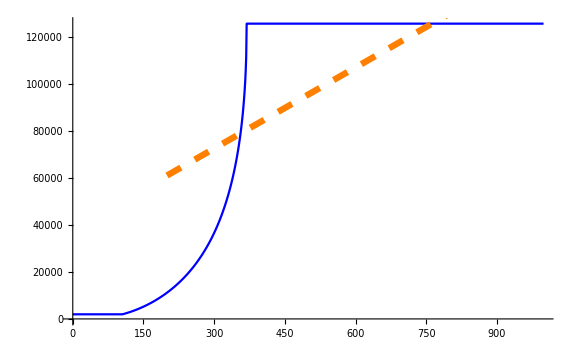

```mathematica
maxT =tMax;
timeList = Range[maxT]-1 ;
data = Transpose[{timeList,areaList[[1;;maxT]]}];

tFit1=200;
tFit2=tMax;
nlm=NonlinearModelFit[data[[tFit1;;tFit2]],a*x+b,{a,b},x];
Print["a is ",a/.nlm["BestFitParameters"]];


Show[ 
ListPlot[data,Joined->True, PlotStyle->Directive[Blue], ImageSize->Large,PlotRange->Full, FrameLabel->{"Time (s)", "Area (μm^2)"}],
Plot[nlm[x],{x,tFit1,tFit2},PlotStyle->{Dashing[0.02],Orange,Thickness[0.008]}]]
```

```mathematica
r0s = {50,40, 30, 20, 10};
gFacs= PowerRange[10^-3,10^0,10^(1/4)];
aList = {};

pList = {};
th = 0.004;

r0 = 25;

DD = 2;
gFac = 1*10^0;
γ=gFac*0.2;
γoff=gFac*0.1;

Do[
(*r0 = r0s[[i]];*)
gFac = gFacs[[i]];
γ=gFac*0.2;
γoff=gFac*0.1;
sol = NDSolve[
{D[CC[r,t],t]==DD*(D[CC[r,t],{r,2}]+1/r D[CC[r,t],{r,1}])-γ*CC[r,t]+γoff*CB[r,t],
D[CB[r,t],t]==γ*CC[r,t]-γoff*CB[r,t],
CB[r,0]==0,
CC[r,0]==Ci0*Exp[(-(r-r0)^2)/2],
CC[r0,t]==Ci0,
CC[rMax,t]==0},{CC,CB},{r,r0,rMax},{t,0,tMax},
PrecisionGoal->6,
AccuracyGoal->6,
MaxSteps->1000000];
CCSol[r_,t_]:=CC[r,t]/.sol;
CBSol[r_,t_]:=CB[r,t]/.sol;

areaList = {};
start = r0;
Do[
rV = RadiusFunction[CBSol, t, 0.5,False,start, 0.9, 1.1];
AppendTo[areaList,Pi*rV^2];
If[rV < 10,start = r0,
start = rV];
,{t,0,tMax,1}];

maxT =tMax;
timeList = Range[maxT]-1 ;
ys = areaList[[1;;maxT]];
ys = Sqrt[ys];
data = Transpose[{timeList,ys}];

tFit1=200;
tFit2=tMax;
nlm=NonlinearModelFit[data[[tFit1;;tFit2]],a*x+b,{a,b},x];
ae= a/.nlm["BestFitParameters"];
AppendTo[aList,ae];
Print["a is ",ae];

AppendTo[pList, 
Show[
ListPlot[data,Joined->True, PlotStyle->Directive[Thickness[th],ColorData["DarkRainbow",( i-1)/(5-1)]], ImageSize->Large, PlotRange->{0,150},FrameLabel->{"Time", "Area"}],
Plot[nlm[x],{x,tFit1,tFit2},PlotStyle->{Dashing[0.02],Orange,Thickness[0.008]}]
]
];


,{i,1,Length[gFacs]}]
```

a is 1.87683×10^-17

a is 1.87683×10^-17

a is 0.00125496

a is 0.0300521

a is 0.0491609

a is 0.0491362

a is 0.0446371

a is 0.0411118

a is 0.0390615

a is 0.0377843

a is 0.0369069

a is 0.0363477

a is 0.0360217

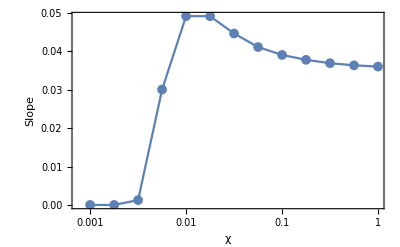

```mathematica
ListLogLinearPlot[Transpose[{gFacs,aList}], Frame->True, FrameLabel->{"χ","Slope"},Joined->True,PlotMarkers->{Automatic,Medium}]
```

```mathematica
legend=LineLegend[
Table[Directive[Thickness[th],ColorData["DarkRainbow",( i-1)/(Length[r0s]-1)]],{i,1,Length[r0s]}]
,r0s,LegendLayout->"Row", LegendLabel->"r_0",LabelStyle->{FontSize->16}];
```

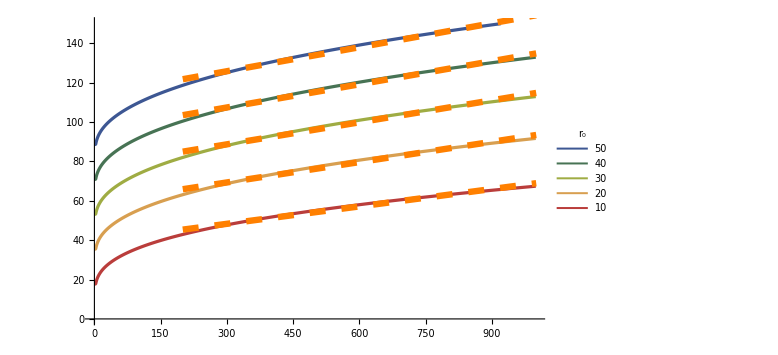

```mathematica
Legended[Show[pList],Placed[legend,{{0.5,0.97},{0.5,0.9}}]]
```

```mathematica
Reverse[aList]
```

{0.0291074,0.0340306,0.0368756,0.0387964,0.0401996}

```mathematica
rData = {10,20,30,40,50};
slopesp5=Transpose[{rData,}];
slopes1=Transpose[{rData,}];
slopes2=Transpose[{rData,{0.029107363493263542,0.03403061768419863,0.03687563325412038,0.03879636975529462,0.040199575224703646}}];
slopes3=Transpose[{rData,}];
slopes4=Transpose[{rData,}];
slopes5=Transpose[{rData,}];
```

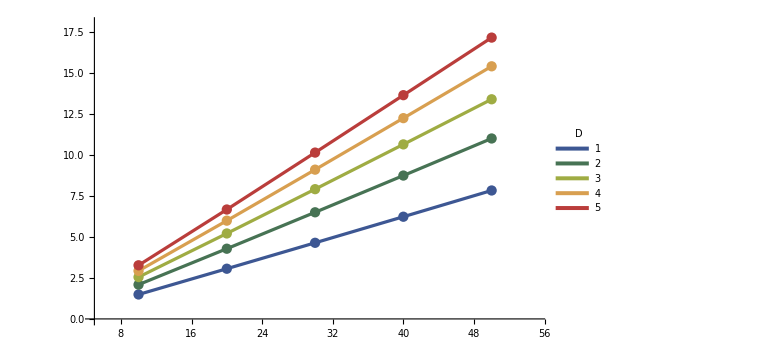

```mathematica
(*rData = {10,20,30,40,50};
slopesp5=Transpose[{rData,{1.07,2.18,3.31,4.43,5.57}}];
slopes1=Transpose[{rData,{1.49,3.06,4.64,6.23,7.83}}];
slopes2=Transpose[{rData,{2.09, 4.28, 6.50, 8.74, 11.00}}];
slopes3=Transpose[{rData,{2.55, 5.21, 7.91, 10.64, 13.39}}];
slopes4=Transpose[{rData,{2.93,5.99,9.10,12.24,15.40}}];
slopes5=Transpose[{rData,{3.27, 6.67, 10.14, 13.64, 17.15}}];*)

legend=LineLegend[
Table[Directive[Thickness[2*th],ColorData["DarkRainbow",( i-1)/(5-1)]],{i,1,5}]
,{1,2,3,4,5},LegendLayout->"Row", LegendLabel->"D",LabelStyle->{FontSize->16}];

Legended[
Show[
ListLinePlot[{slopes1,slopes2, slopes3, slopes4, slopes5}, FrameLabel->{"r_0", "Slope"}, PlotRange->{{5, 55},{0, 18}}, ImageSize->Large,PlotStyle->Table[Directive[Thickness[th],ColorData["DarkRainbow",( i-1)/(5-1)]],{i,1,5}]],
ListPlot[{slopes1,slopes2, slopes3, slopes4, slopes5},PlotStyle->Table[Directive[ColorData["DarkRainbow",( i-1)/(5-1)]],{i,1,5}]]],Placed[legend,{{0.3,0.97},{0.5,0.9}}]]
```

```mathematica
LinearModelFit[slopesp5,x,x]
```

FittedModel[-0.063+0.1125 x]

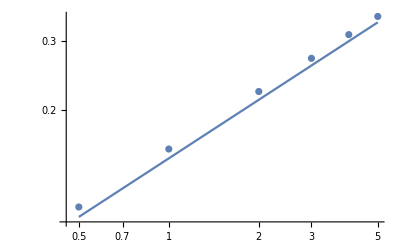

```mathematica
ds={0.5,1,2,3,4,5};
Show[ListLogLogPlot[Transpose[{ds,{0.1125,0.1585, 0.2228, 0.2711,0.3119,0.3473}}]],
LogLogPlot[0.15*x^(1/2),{x,0.5,5}]
]
```

```mathematica
Sqrt[0.5]
```

0.707107

```mathematica
(*CCsol = NDSolveValue[
{D[CC[r,t],t]==DD*(D[CC[r,t],{r,2}]+1/r D[CC[r,t],{r,1}])-kOn * BS[BB[r,t]]*CC[r,t]+kOff *BB[r,t],
D[BB[r,t],t]==kOn * BS[BB[r,t]]*CC[r,t]-kOff *BB[r,t],
CC[r,0]==Ci0*Exp[(-(r-r0)^2)/2],
CC[r0,t]==Ci0,
CC[rMax,t]==0,
BB[r,0]==Bi0},{CC,BB},{r,r0,rMax},{t,0,tMax},
PrecisionGoal->8,
AccuracyGoal->8,
MaxSteps->1000000];*)

(*
CCsolApprox = NDSolveValue[
{D[CC[r,t],t]==frac[CC[r,t],BB[r,t]]*DD*(D[CC[r,t],{r,2}]+1/r D[CC[r,t],{r,1}]),
D[BB[r,t],t]==(1-frac[CC[r,t],BB[r,t]])*DD*(D[CC[r,t],{r,2}]+1/r D[CC[r,t],{r,1}]),
CC[r,0]==frac[Ci0*Exp[(-(r-r0)^2)/2],Bi0]*(Ci0*Exp[(-(r-r0)^2)/2]+Bi0)+10^-4,
BB[r,0]==(1-frac[Ci0*Exp[(-(r-r0)^2)/2],Bi0])*(Ci0*Exp[(-(r-r0)^2)/2]+Bi0)+10^-4,
CC[r0,t]==frac[Ci0*Exp[(-(r0-r0)^2)/2],Bi0]*(Ci0*Exp[(-(r0-r0)^2)/2]+Bi0)+10^-4,
CC[rMax,t]==frac[Ci0*Exp[(-(rMax-r0)^2)/2],Bi0]*(Ci0*Exp[(-(rMax-r0)^2)/2]+Bi0)+10^-4

},{CC,BB},{r,r0,rMax},{t,0.0,tMax},Method->{"MethodOfLines","TemporalVariable"->t,
"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->120,"MaxPoints"->pts,"DifferenceOrder"->2},
Method->{"IDA","ImplicitSolver"->{"GMRES"}}},
PrecisionGoal->8,
AccuracyGoal->8,
MaxSteps->1000000];*)
```

General::munfl: Exp[-11250.] is too small to represent as a normalized machine number; precision may be lost.

NDSolveValue::mxsst: Using maximum number of grid points 5000 allowed by the MaxPoints or MinStepSize options for independent variable r.